## Боровский М.В.

## Лабораторная работа №5 : Численные расчёты в системе Mathematica

## 5.1

#### 5.1.а | Пробел выполняет роль знака умножения

```mathematica
3 5
```

15

#### 5.1.б | Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
3   5
```

15

```mathematica
2+         7
```

9

#### 5.1.в | Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя

```mathematica
2/3
```

2/3

```mathematica
17^(1/2)
```

√17

#### 5.1.г | Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды

```mathematica
3 /7.
```

0.428571

```mathematica
17.^(1/2)
```

4.12311

#### 5.1.д | Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
5     (4-1)
```

15

## 5.2

#### 5.2.а | С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17],200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

#### 5.2.б | Найти приближенное значение числа с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа

```mathematica
N[E^(Pi*Sqrt[163]),40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[N[E^(Pi*Sqrt[163]),40]] - N[E^(Pi*Sqrt[163]),40]
```

7.499274028×10^-13

#### 5.2.в | Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

#### 5.2.г | Последовательно введите выражения | Справедливо ли неравенство

```mathematica
5>3
```

True

```mathematica
5<2
```

False

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E]
```

```mathematica
22.45915771836104
```

22.4592

```mathematica
N[E^Pi]
```

23.1407

## 5.3

#### 5.3.а | Решить уравнения

```mathematica
NSolve[Sqrt[x+2]+4*x==4,x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5== 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

```mathematica
x^3-3  x^2 /. %[[2]]
```

-5.-8.88178×10^-16 ⅈ

#### 5.3.б | Решить системы уравнений

```mathematica
NSolve[{x^2+x*y+y^2==1,x^3+x^2*y+x*y^2+y^3==4},{x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
x^2+x*y+y^2/.%[[2]]
```

1.+2.22045×10^-15 ⅈ

```mathematica
NSolve[{x-y^2+3*z==34,x+y-z==-1,-x+2*y+3*z==4},{x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

#### 5.3.в | Придумать уравнение или систему уравнений и найдите её численное решение

```mathematica
NSolve[{x^3+y^3+3*x^2*y+3*y^2*x==64,x+3*y==8}, {x,y},Reals]
```

{{x→2.,y→2.}}

## 5.4

#### Вариант 3 -Graphics-

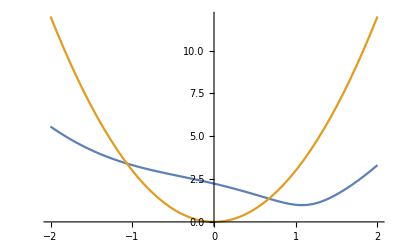

```mathematica
Plot[{Sqrt[x^4-5*x+5], 3*x^2}, {x, -2,2}]
```

```mathematica
FindRoot[Sqrt[x^4-5*x+5]== 3*x^2, {x, 0.7}]
```

{x→0.672582}

```mathematica
FindRoot[Sqrt[x^4-5*x+5]== 3*x^2, {x, -1.1}]
```

{x→-1.06599}

## 5.5

#### Вариант 3 -Graphics-

```mathematica
funcy=NDSolve[{y''[x]+ Cos[x]y[x]+x^2==0,y[0]==1,y'[0]==1},y,{x,-2,3}]
```

{{y→InterpolatingFunction[…]}}

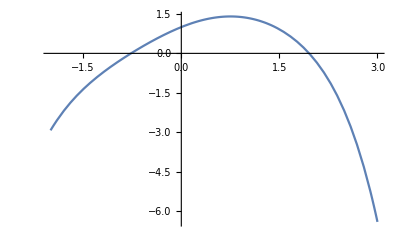

```mathematica
Plot[y[x]/.funcy,{x,-2,3}]
```

#### 5.5.a | Найдите на заданном отрезке корни уравнения y(x)=0

```mathematica
r1=FindRoot[y[x]/.funcy,{x,-0.8}]
```

{x→-0.769497}

```mathematica
r2=FindRoot[y[x]/.funcy,{x,1.9}]
```

{x→1.95491}

#### 5.5.б | Найдите значения производной y’(x) в точках, где y(x)=0

```mathematica
D[y[x]/.funcy,x]/.r1
```

{1.54188}

```mathematica
D[y[x]/.funcy,x]/.r2
```

{-2.7395}

#### 5.5.в | Выберите одну из точек, в которых производная функции y(x)=0, и вычислите значение функции в этой точке

```mathematica
LocalMaxim=FindRoot[D[y[x]/.funcy,x]==0,{x,0.8}]
(*Производная равна 0 в точках где касательная к графику функции паралельна оси абсцисс(точки экстремума)*)
```

{x→0.752417}

```mathematica
y[x]/.funcy/.LocalMaxim
```

{1.4042}

#### 5.5.г | С помощью функции FindMinimum найдите точки, в которых функция y(x) имеет локальный минимум или максимум, и сравните полученные результаты со значениями, найденными в пункте ‘в’

```mathematica
FindMaximum[y[x]/.funcy,{x,0.8}]x
```

{1.4042,{x→0.752417}}

## 5.6

#### 5.6.а | Задайте произвольные численные значения параметров a,b,c,d,e в следующих зависимостях: y(x)=a+b*x+c*x^2+d*x^3+e*x^4 и y(x)=a+b*x+c*sin(x)+d*cos(x). Используя функцию Table, определите список численных данных, каждый элемент которого содержит два элемента (x,y). Область изменения х и шаг выберите самостоятельно. С помощью функции Random внесите в каждой точке х случайное возмущение Дy

#### 1)

```mathematica
dat1=Table[{x,(10+8*x+6*x^2+4*x^3+2*x^4)(1+Random[Real,{-0.1,0.1}])},{x,0,4,0.2}]
```

{{0.,10.9077},{0.2,11.7251},{0.4,14.6644},{0.6,18.6509},{0.8,21.2998},{1.,30.1291},{1.2,43.0741},{1.4,56.1152},{1.6,61.7624},{1.8,85.6787},{2.,122.711},{2.2,145.262},{2.4,176.92},{2.6,238.626},{2.8,300.521},{3.,388.392},{3.2,442.135},{3.4,566.189},{3.6,691.997},{3.8,783.4},{4.,857.287}}

#### 2)

```mathematica
dat2=Table[{x,(20+38*x+62*Sin[x]+25*Cos[x])(1+Random[Real,{-0.1,0.1}])},{x,0,5,0.2}]
```

{{0.,48.8416},{0.2,70.4062},{0.4,80.7507},{0.6,94.057},{0.8,112.07},{1.,121.119},{1.2,138.927},{1.4,129.359},{1.6,155.354},{1.8,140.701},{2.,150.752},{2.2,127.994},{2.4,137.591},{2.6,130.223},{2.8,119.592},{3.,125.85},{3.2,124.1},{3.4,116.96},{3.6,105.081},{3.8,102.069},{4.,101.324},{4.2,123.326},{4.4,127.336},{4.6,118.712},{4.8,135.177},{5.,172.693}}

#### 5.6.б | Изобразите полученные точки на координатной плоскости

```mathematica
1)
```

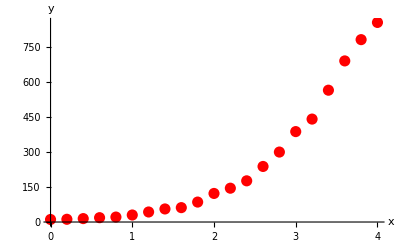

```mathematica
y1=ListPlot[dat1,PlotStyle->{PointSize[0.02], Red},AxesLabel->{"x","y"}]
```

```mathematica
2)
```

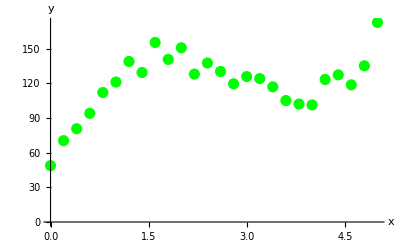

```mathematica
p1=ListPlot[dat2,PlotStyle->{PointSize[0.02],Green},AxesLabel->{"x","y"}]
```

#### 5.6.в | С помощью функции Fit найдите наилучшую кривую, аппроксимирующую численные данные

```mathematica
1)
```

```mathematica
apr1=Fit[dat1,{1,x,x^2,x^3,x^4},x]
```

1.12021+87.6905 x-109.091 x^2+56.6312 x^3-5.27122 x^4

```mathematica
apr2=Fit[dat1,{1,x,Sin[x],Cos[x], Sin[2x], Cos[2x]},x](*экспериментальные точки*)
```

3.18352+172.001 x+56.2879 Cos[x]-44.3001 Cos[2 x]-249.451 Sin[x]+20.2959 Sin[2 x]

```mathematica
2)
```

```mathematica
aproc1=Fit[dat2,{1,x,Sin[x],Cos[x]},x]
```

16.3498+39.3325 x+26.1953 Cos[x]+63.98 Sin[x]

```mathematica
aproc2=Fit[dat2,{1,x,x^2,x^3,x^4,x^5},x](*экспериментальные точки*)
```

48.5979+93.6127 x-10.5502 x^2-11.5258 x^3+2.88443 x^4-0.143923 x^5

#### 5.6.г | На одной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками

```mathematica
1)
```

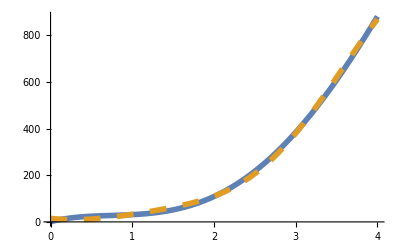

```mathematica
y2=Plot[{apr1,apr2},{x,0,4},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

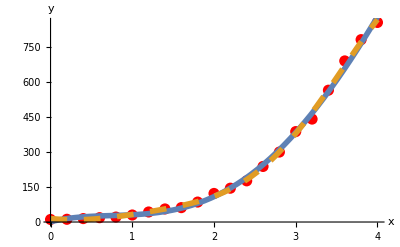

```mathematica
Show[y1,y2]
```

```mathematica
2)
```

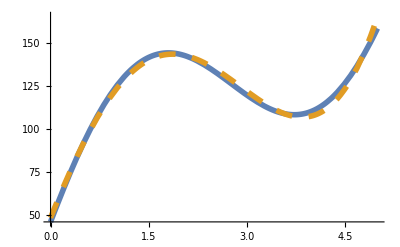

```mathematica
p2=Plot[{aproc1,aproc2},{x,0,5},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

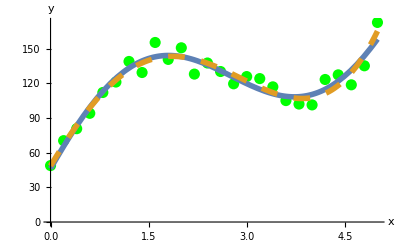

```mathematica
Show[p1,p2]
```